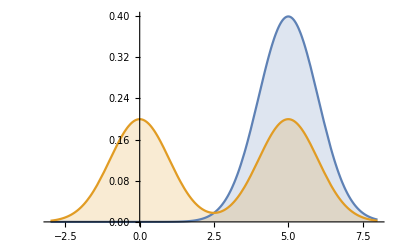

```mathematica
d1 = NormalDistribution[0,1];
d2 = NormalDistribution[5,1];
d3 = MixtureDistribution[{.5,.5},{d1,d2}];
Plot[{PDF[d2,x],PDF[d3,x]},{x,-3,8},Filling->Axis]
```

```mathematica
klDivergence[d1_,d2_] := NExpectation[Log[PDF[d1,x]/PDF[d2,x]],x\[Distributed]d1]
```

```mathematica
p = MixtureDistribution[{.5,.5},{d1,d2}];
```

```mathematica
Manipulate[TableForm[{q=NormalDistribution[μ,σ];Plot[{PDF[p,x],PDF[q,x],Log[PDF[p,x]/PDF[q,x]],Log[PDF[q,x]/PDF[p,x]]},{x,-3,8},Filling->Axis],klDivergence[p,q],klDivergence[q,p]},],{μ,-1,7},{σ,.001,6}]
```

General::munfl: Exp[-2.×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-9.245×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.